```mathematica
e=1;
m=2;
P=4;
Ep=1;
Pfinal=6;
var=Table[0,{e,1,Ep}];
varr=Table[0,{i,1,Pfinal-P}];
```

```mathematica
(Label[New];
n=101;
S=2;
t=1;
T=50P;
mu=Table[0,{i,1,T}];
PayoffFunction=Table[0,{i,1,n},{s,1,S}];
bestStrategy=Table[0,{i,1,n}];
U=Table[1,{i,1,n},{i,1,S}];
AgentStrategy=Table[0,{i,1,n},{i,1,S}];
A=Table[0,{i,1,T}];
"initial set";
mu⟦1⟧=RandomInteger[P-1];AgentStrategy=Table[RandomChoice[{1,-1}],{n},{S},{P}];
Do[bestStrategy⟦i⟧=Flatten[RandomChoice[AgentStrategy⟦i⟧,1]],{i,1,n}];
Label[begin];
"Nature choice";
mu⟦t⟧=RandomInteger[P-1];
"Agents choice";
Do[bestStrategy⟦i⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
"Market interaction,A(t)=Σ_(i = 1)^na_(i, s*)(t)";
MarketAction=0;
Do[MarketAction=MarketAction+bestStrategy⟦i⟧⟦mu⟦t⟧+1⟧,{i,1,n}];
A⟦t⟧=MarketAction;
"Agents learning";
Do[PayoffFunction⟦i,s⟧=-(AgentStrategy⟦i,s⟧⟦mu⟦t⟧+1⟧)(A⟦t⟧),{s,1,S},{i,1,n}];
Do[U⟦i,s⟧=U⟦i,s⟧+PayoffFunction⟦i,s⟧,{s,1,S},{i,1,n}];
t=t+1;
"Go on or Stop";
If[t>T,Goto[sample],Goto[begin]];
Label[sample];var⟦e⟧=Variance[A];
e=e+1;
If[e>Ep,Goto[next],Goto[New]];
Label[next];
varr⟦P-3⟧={P/n,Mean[var]/n};
P=P+1;
e=1;
If[P==Pfinal,Break,Goto[New]];
)//AbsoluteTiming
```

{1.31107,Null}

```mathematica
N[varr]
```

{{0.039604,6.40254},{0.049505,6.45727}}

```mathematica
"Anylize";
random=Table[{i/50,1},{i,1,10}];
```

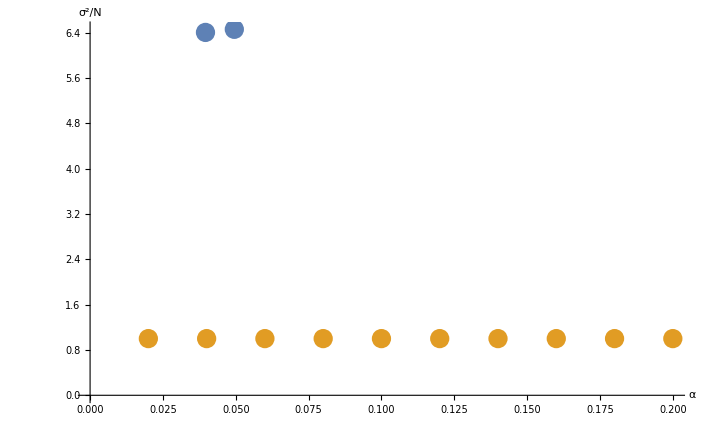

```mathematica
f1=ListPlot[{varr,random},AxesLabel->{"α","σ^2/N"}]
```